```mathematica
Lab №2
```

№2 Lab

{{-17,-7},{-16,10},{-10,12},{-7,10},{-3,5},{1,-3},{4,13},{12,-13},{5,-19}}

{{2,-7}}

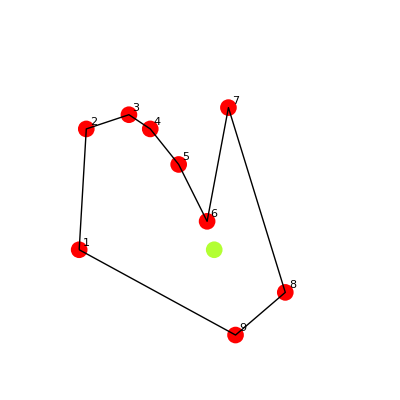

```mathematica
MPolinom = {{-17,-7},{-16,10},{-10,12},{-7,10},{-3,5},{1,-3},{4,13},{12,-13},{5,-19}}
MPoint ={{2,-7}}
Graphics[{PointSize[0.03],RGBColor[.7, 5, .2], Point[MPoint], PointSize[0.03], Red, Point/@MPolinom, Black, MapIndexed[Text[#2⟦1⟧, #1+{1,1}]&,MPolinom], Line[Append[MPolinom, MPolinom⟦1⟧]]}, AspectRatio->Automatic, PlotRange->{{-23, 23},{-23,23}}]
```

```mathematica
xMin = Min [Table[MPolinom[[i]][[1]], {i, 1,  Length[MPolinom]}]];
yMin = Min [Table[MPolinom[[i]][[2]], {i, 1,  Length[MPolinom]}]];
xMax = Max[Table[MPolinom[[i]][[1]], {i, 1,  Length[MPolinom]}]];
yMax = Max [Table[MPolinom[[i]][[2]], {i, 1,  Length[MPolinom]}]];
```

```mathematica
xMin
xMax
yMin
yMax
```

-17

12

-19

13

```mathematica
MPoint[[1,2]]
If[MPoint⟦1,1⟧<xMin || MPoint⟦1,1⟧>xMax||MPoint⟦1,2⟧<yMin || MPoint⟦1,2⟧>yMax, Print["Точка лежит вне полинома"]]



PointOnLine[{p1_, p2_}, p0_]:=Det[{p2-p1,p0-p1}]==0
SecondPoint = {-20};
AppendTo[SecondPoint, MPoint⟦1,2⟧];
SecondPoint
```

-7

{-20,-7}

```mathematica
SecondLine = {};
AppendTo[SecondLine,SecondPoint];
AppendTo[SecondLine,MPoint⟦1⟧];
SecondLine
```

{{-20,-7},{2,-7}}

```mathematica
For[i = 1, i<10, i++,{If[PointOnLine[SecondLine,MPolinom⟦i⟧],{SecondLine  = Delete[SecondLine,{1,2}], AppendTo[SecondLine⟦1⟧, Random[Integer, {-20, 20}]], i=1}]}]
```

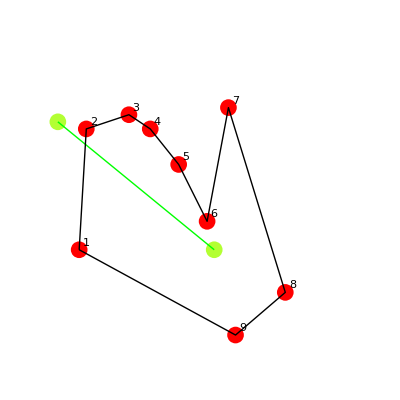

```mathematica
Graphics[{PointSize[0.03],RGBColor[.7, 5, .2], Point/@SecondLine, Green, Line[SecondLine], PointSize[0.03], Red, Point/@MPolinom, Black, MapIndexed[Text[#2⟦1⟧, #1+{1,1}]&,MPolinom], Line[Append[MPolinom, MPolinom⟦1⟧]]}, AspectRatio->Automatic, PlotRange->{{-23, 23},{-23,23}}]
```

```mathematica
ICount = 0;
n=1;
While[n<9, {
d1 = Det[{MPolinom⟦n+1⟧-MPolinom⟦n⟧,SecondLine⟦1⟧-MPolinom⟦n⟧}];
d2 = Det[{MPolinom⟦n+1⟧-MPolinom⟦n⟧,SecondLine⟦2⟧-MPolinom⟦n⟧}];
d3 = Det[{SecondLine⟦2⟧-SecondLine⟦1⟧,MPolinom⟦n⟧-SecondLine⟦1⟧}];
d4 = Det[{SecondLine⟦2⟧-SecondLine⟦1⟧,MPolinom⟦n+1⟧-SecondLine⟦1⟧}];
If[d1*d2≤0 && d3*d4 ≤0,ICount ++]}n++]
```

```mathematica
d1 = Det[{MPolinom⟦9⟧-MPolinom⟦1⟧,SecondLine⟦1⟧-MPolinom⟦1⟧}];
d2 = Det[{MPolinom⟦9⟧-MPolinom⟦1⟧,SecondLine⟦2⟧-MPolinom⟦1⟧}];
d3 = Det[{SecondLine⟦2⟧-SecondLine⟦1⟧,MPolinom⟦9⟧-SecondLine⟦1⟧}];
d4 = Det[{SecondLine⟦2⟧-SecondLine⟦1⟧,MPolinom⟦9⟧-SecondLine⟦1⟧}];
If[d1*d2≤0 && d3*d4 ≤0,ICount ++]
ICount
```

1

```mathematica
If[Mod[ICount,2]==1, "Точка лежит внутри полигона", "Точка лежит снаружи полигона"]
```

Точка лежит внутри полигона